```mathematica
allFiles=FileNames["*.m",NotebookDirectory[]<>"weaveMaps/"];
```

This is an implementation of the pre-processing algorithm to clean up the images.

```mathematica
clean[matrix_]:=Module[{},
Return[ArrayPlot[matrix, ColorFunction->"ThermometerColors"]];
(*Return[ImageAdjust[Image[CommonestFilter[matrix,{3,0}]]]];*)
];
clean[test1]
```

-Graphics-

This is a helper function to the distWeaveMapsZJ method that finds the minimum distance across all possible relative row placements (see below for further description).

```mathematica
minRowOverlap::usage="This function takes as input two rows of two images, then considers all possible overlaps between them and outputs the overall minimum distance based on some appropriate metric (EuclideanDistance for instance)"

minRowOverlap[row1_, row2_]:= Module[{},
	
	numCols1 = Length[row1];
	numCols2 = Length[row2];

	If[numCols1 ≥ numCols2,smallCol = row2; largeCol = row1, smallCol = row1; largeCol = row2];

	(*This is the maximum number of overlaps*)
	numPlaces = Length[largeCol]-Length[smallCol]+ 1;

	(*This adjust how many overlaps we actually compare. To increase speed of algorithm, we avoid comparing overlaps 
	that are too similar to each other by setting jumpSize > 1 *)
	jumpSize = 10;
	min = Power[10,10];
	imin = 0;
	

	For[j=1, j<= numPlaces, j=j+jumpSize,

		rowsLargeCol = largeCol[[j;;j+Length[smallCol]-1]];
		d = EuclideanDistance[rowsLargeCol,smallCol];

		If[d<min, min=d; imin = j;];	
];

(*Function outputs smallest distance across all overlaps used*)
Return[{d,imin}]
	
]
```

This function takes as input two rows of two images, then considers all possible overlaps between them and outputs the overall minimum distance based on some appropriate metric (EuclideanDistance for instance)

This function computes the distance between two images by using the overlaps given by the variable subset.

```mathematica
compare::usage="This function calculates the minimum distance between two images over a subset of possible overlaps without changing the orientation of the image. The input is assumed to be two images with horizontal stripes, and the output consist of the minimum distance and the overlap that gives the minimum distance. This function is used in as a helper in compareAll method in order to account for all possible orientations."

compare[im1_,im2_, subset_]:=Module[{},

numRows1 = Dimensions[im1][[1]];
numRows2 = Dimensions[im2][[1]];

(*This is the index when the overlaps ends*)
end = Min[numRows1,numRows2];
dmin = Power[10,10];
index = 0;

For[i=1,i≤Dimensions[subset][[1]],i++,
ind1 = subset[[i,2]];
ind2 = subset[[i,3]];
begin = Abs[ind1-ind2];

(*In order to improve accuracy, the function EarthMoverDistance can be changed to some other metric*)
If[ind1≥ind2,
d = ImageDistance[clean[im1[[begin;;end,All]]],clean[im2[[1;;end,All]]], DistanceFunction->"EarthMoverDistance"];];

If[ind1<ind2,
 d = ImageDistance[clean[im1[[begin;;end,All]]],clean[im2[[1;;end,All]]], DistanceFunction->"EarthMoverDistance"];
 ];
 
d = d/(end);
If[d<dmin, dmin = d; index = i;]
];

(*The function returns the minimum distance and the index to subset that contains overlaps that causes the minimum distance*)
Return[{dmin, index}];
]
```

This function calculates the minimum distance between two images over a subset of possible overlaps without changing the orientation of the image. The input is assumed to be two images with horizontal stripes, and the output consist of the minimum distance and the overlap that gives the minimum distance. This function is used in as a helper in compareAll method in order to account for all possible orientations.

{249,323}

{304,366}

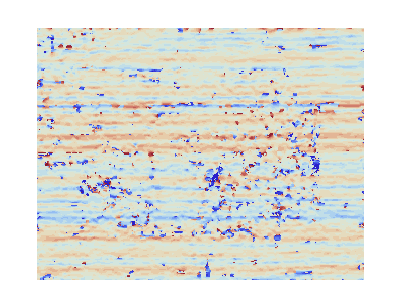

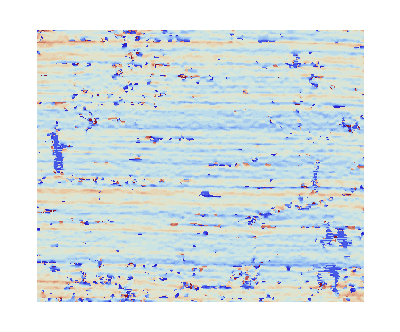

```mathematica
Get[allFiles[[5]]];
test1 = Transpose[matV];
Get[allFiles[[6]]];
test2 = matH;

Dimensions[test1]
Dimensions[test2]
clean[test1]
clean[test2]
```

```mathematica
findOverlap::usage="This function finds the best overlap (in the sense that the distance between images is the smallest) between two images. It does this by finding the pair of rows that have the smallest distances. It returns a subset of these rows containing information about their position relative to the original image. The output has num rows and each row contains the coordinates of one possible overlab (coordinates of row within image)"

findOverlap[im1_,im2_, num_]:=Module[{},
dmin = Power[10,10];
imin = 0;
jmin = 0;
minArray = ConstantArray[0,{num,3}];
minArray[[1;;num,1]]=dmin;


(*Avoids overlaps that are too small*)
thresh =Floor[Min[Dimensions[im1][[1]], Dimensions[im2][[1]]]/3];

(*Iterates through rows of im1 and im2*)
For[c1=thresh, c1≤Dimensions[im1][[1]]-thresh,c1++,
If[Divisible[c1,100],Print[c1]];

For[c2=1,c2≤ Dimensions[im2][[1]],c2++,

{d,index} = minRowOverlap[im1[[c1,All]],im2[[c2,All]]];

(*Update array of minimum distances*)
For[c3=1,c3≤num,c3++,
If[d<minArray[[c3,1]],
minArray[[c3,1]]=d;
minArray[[c3,2]]=c1;
minArray[[c3,3]]=c2;
Break[];
];
];

];
];
Return[minArray];
];
minArray =findOverlap[test1,test2,4]
Print[minArray];
```

This function finds the best overlap (in the sense that the distance between images is the smallest) between two images. It does this by finding the pair of rows that have the smallest distances. It returns a subset of these rows containing information about their position relative to the original image. The output has num rows and each row contains the coordinates of one possible overlab (coordinates of row within image)

200

300

{{4.04554,308,149},{4.18254,147,146},{4.1839,147,306},{4.18778,308,303}}

{{4.04554,308,149},{4.18254,147,146},{4.1839,147,306},{4.18778,308,303}}

```mathematica
compare[test1,test2,minArray]
```

{0.000216593,4}

```mathematica
horizontal::usage="This function takes an image as input and ouputs the image rotated so that its stripes are horizontal"

horizontal[canvas_]:=Module[{},
lines =ImageLines[EdgeDetect[clean[canvas],1,0.1],MaxFeatures->100];
verticalCount=0;

	For[i=1,i≤Length[lines],i++,
	current=lines[[i,1]];
	
	If[Abs[current[[1,2]]-current[[2,2]]]>1 && Abs[current[[1,1]]-current[[2,1]]] < 100,
	verticalCount++;];
];
(*Depending on whether most lines are horizontal or vertical, output original or rotated image*)
If[verticalCount>Length[lines]/2,
Return[Transpose[canvas]];,
Return[canvas];]
];
```

This function takes an image as input and ouputs the image rotated so that its stripes are horizontal

```mathematica
compareAll::usage="Considers all possible orientations of images and computes minimum distance using compare method. Assumes input to have horizontal lines and uses compare method to calculate the distance using each overlap."

compareAll[im1_,im2_, subset_]:=Module[{},

(*We fix im1 and rotate im2 appropriately to account for all possible orientations*)
r1 = Reverse[test2];
r2 = Transpose[Reverse[Transpose[test2]]];
r3 = Transpose[Reverse[Transpose[Reverse[test2]]]];

(*Since subset1=subset3, subset2=subset*)
subset1=subset;
For[t=1,t≤Length[subset],t++,
subset1[[t,3]]= Dimensions[im2][[1]]-Abs[ Dimensions[im2][[1]]-subset[[t,3]]];
];

(*will need to change subset appropriately*)
{d,index} = compare[im1,im2,subset];
{d1,index} = compare[im1,r1,subset1];
{d2,index} = compare[im1,r2,subset];
{d3,index} = compare[im1,r3,subset1];
min = Min[d,d1,d2,d3];

(*make sure to output correct alignment coordinates*)
minSubset=subset;
If[d1==min,minSubset = subset1];

orientation = 0;
(*make sure to output correct orientation alignment, 
orientation = 0 corresponds to no rotation, 1 to r1, 2 to  r2 and 3 to r3*)
If[d1==min,orientation = 1];
If[d2==min,orientation = 2];
If[d3==min,orientation = 3];


Return[{min,minSubset, orientation, index}]

];
```

Considers all possible orientations of images and computes minimum distance using compare method. Assumes input to have horizontal lines and uses compare method to calculate the distance using each overlap.

```mathematica
distWeaveMapsZJ[canvas1_, canvas2_]:=Module[{},

(*Reduce amount of noise in both images*)

(*Ensure that both inputs are oriented with horizontal stripes*)
canvas1H = horizontal[canvas1];
canvas2H = horizontal[canvas2];

(*Find the rows that are the most similar between two canvases*)
minArray = findOverlap[canvas1H, canvas2H, 4];

(*Compute the distance between images using all overlaps in minArray and pick the one with smallest distance*)
{dmin, minSubset,orientation,index} = compareAll[canvas1H,canvas2H, minArray];

Return[{dmin,minSubset,orientation,index}];
];

Get[allFiles[[3]]];
test1 = matV;
Get[allFiles[[4]]];
test2 = matV;

{dmin,minSubset,orientation,index} =distWeaveMapsZJ[test1,test2]
```

200

300

{0.0000773531,{{4.04554,308,149},{4.18254,147,146},{4.1839,147,306},{4.18778,308,303}},2,1}

We display the results below:

```mathematica
test2 = horizontal[test2];
r1 = Reverse[test2];
r2 = Transpose[Reverse[Transpose[test2]]];
r3 = Transpose[Reverse[Transpose[Reverse[test2]]]];
test1 = horizontal[test1];

ref1 = Line[{{0,minSubset[[index,2]]},{Dimensions[test1][[2]],minSubset[[index,2]]}}];
ref2 = Line[{{0,minSubset[[index,3]]},{Dimensions[r2][[2]],minSubset[[index,3]]}}];
```

```mathematica
GraphicsRow[{Show[clean[test1],Graphics[{Black,ref1}]], Show[clean[r2],Graphics[{Black,ref2}]]}]
```

-Graphics-

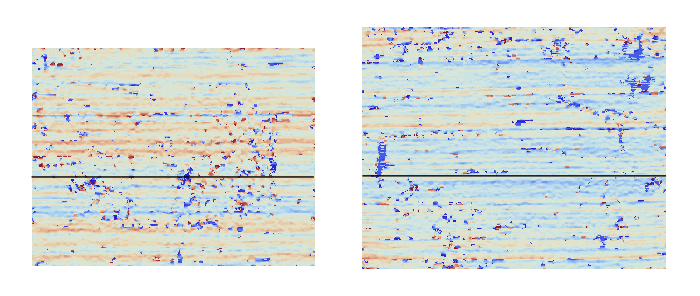

```mathematica
-Graphics--Graphics-
```